# Mathematica Plotting and Manipulate

### Plotting Functions

Mathematica contains a plethora of graphing functions: 
Plot
 PolarPlot
 ListPlot
 Plot3D
 ParametricPlot
  LogPlot 
  ListLinePlot
  LogLogPlot
  ContourPlot
  The list goes on and on....
  
  One great and quite way to visualize physical problems is to use one of the plotting tools with Mathematica’s Manipulate Function.

### Listplots

Mathematica allows you to plot analytical functions and lists of numbers

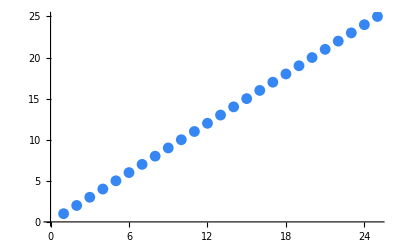

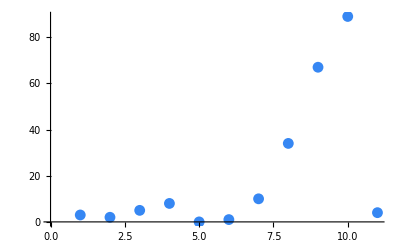

```mathematica
y = Range[25];
y2={3,2,5,8,0,1,10,34,67,89,4};
ListPlot[y]
ListPlot[y2]
```

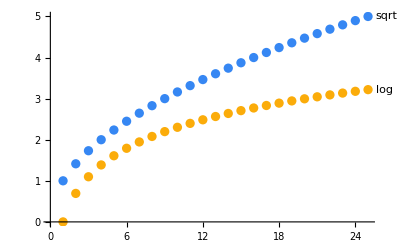

```mathematica
ListPlot[{Labeled[Sqrt[y],"sqrt"],Labeled[Log[y],"log"]}]
```

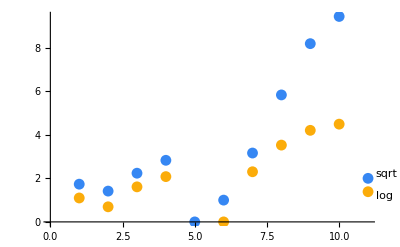

```mathematica
ListPlot[{Labeled[Sqrt[y2],"sqrt"],Labeled[Log[y2],"log"]}]
```

### Elliptical Orbits

Most bodies in our solar system follow an elliptical orbit. We can get an idea about how the eccentricity warps the orbit from a purely circular one by graphing the orbital equations in polar coordinates

```mathematica
Manipulate[PolarPlot[{1/(1+ϵ Cos[ϕ]),1},{ϕ,0,2π}],{ϵ,0,1.5}]
```

### Precession of the Perihelion

The perihelion of many bodies precesses about the elliptical orbit’s focus (a famous example being the precession of Mercury’s perihelion). We can use PolarPlot with Manipulate to visualize this precession.

```mathematica
Manipulate[PolarPlot[{1/(1+ϵ Cos[ϕ+a])},{ϕ,0,2π}, PlotRange->{{-8,8},{-8,8}}],{ϵ,0,1},{a,0,4*π}]
```

### Charged Particles in Electric and Magnetic Fields

Charged particles in a magnetic field undergo circular motion and those in an electric field are acceleration along the field lines. The combined motion can be described as undergoing helical motion. What does that look like?

```mathematica
qm=10;
time[Bx_,By_,Bz_] := (20 π)/(qm*√(Bx^2+By^2+Bz^2));
motion[Ex_,Ey_,Ez_,Bx_,By_,Bz_,vx0_,vy0_,vz0_]:=NDSolve[{vx'[t]==qm*Ex - qm(vy[t]Bz - vz[t]By),vy'[t]==qm*Ey - qm(vz[t]Bx - vx[t]Bz),vz'[t]==qm*Ez - qm(vx[t]By - vy[t]Bx),vx[0]==vx0,vy[0]==vy0,vz[0]==vz0},{vx[t],vy[t],vz[t]},{t,0,time[Bx,By,Bz]}]
```

```mathematica
vel = motion[1,0,0,0.5,0,0,0,2,0]
```

{{vx[t]→InterpolatingFunction[…][t],vy[t]→InterpolatingFunction[…][t],vz[t]→InterpolatingFunction[…][t]}}

```mathematica
vel[[1,1]]
```

vx[t]→InterpolatingFunction[…][t]

```mathematica
ParametricPlot3D[{{vx[t]/.vel[[1,1]],vy[t]/.vel[[1,2]],vz[t]/.vel[[1,3]]},{t,0,0}},{t,0,time[0.5,0,0]}]
```

-Graphics3D-

### Fluid Dynamics

A classic problem in fluid dynamics involves a water tank with diameter d_t and height H and pressurized to a gauge pressure of P. You cut a small hole of diameter d_bin the bottom of the tank.  Using Bernoulli’s principle and the continuity equation, you can express the time it takes to empty such a tank to empty. It should be obvious (if you review the relevant topics) that a tank does not empty as a constant rate, it necessitates calculus. The expression for the rate at which the surface of the water in the tank falls is given by

dh/dt = (√(2 P/ρ+2gh))/((d_t/d_b)^2+1)

To solve such an equation, we need to separate the differentials and integrate

```mathematica
Clear[g]
T[P_,ρ_,dt_,db_,h_]=Integrate[(dt^2/db^2+1)/(√(2*P/ρ+2*g*h)),h]
```

((1+dt^2/db^2) √(2 g h+(2 P)/ρ))/g

We can graph the function T and without filling in the parameters inside Manipulate to see how different parameters affect the time to empty

```mathematica
g=9.81;
Manipulate[Plot[T[P,ρ,dt,db,h],{h,0,1.5},AxesLabel->{"Height (m)","Time to empty (s)"}],{P,0,10000},{ρ,500,1500},{db,1,10},{dt,200,500}]
```

We can even use Manipulate with regular evaluations

```mathematica
Manipulate[(T[P,ρ,dt,db,h]-T[P,ρ,dt,db,0])/60,{P,5000,10000},{ρ,500,1500},{dt,1,50},{db,0.01,0.5},{h,0.1,3.0}]
```

```mathematica
T[5000,1000,1.7,0.014,0.9]/60
```

131.753